# Курсовая работа по теме “Раскраска карт”

## Содержание

## Немного теории и о целях задачи

Как известно, любая карта является плоским объектом, и границы между любыми двумя парами стран не могут пересекаться. То есть, чтобы решить задачу о раскраске карт, нужно, по существу, решить задачу о раскраске планарного, или плоского, графа.
Планарный (плоский) граф — граф, который может быть изображён на плоскости без пересечения его рёбер.
В данном случае карта преобразуется в плоский граф таким образом: каждая страна на карте является вершиной данного графа; любые же две страны (вершины), имеющие на карте общую границу (границей считается продолжительная линия, точка границей не является), соединены ребром.

Задача же раскраски графа заключается в том, что, во-первых, любые две соседние (то есть соединённые ребром) вершины должны иметь разный цвет, а, во-вторых, нужно минимизировать число цветов, использованных для раскраски. Такое число (наименьшее количество цветов, необходимое для раскраски данного графа) также называют хроматическим (обозн.: χ(G), где G - граф).

Для плоского графа справедливо следующее утверждение: хроматическое число любого планарного графа не превосходит четырёх. Альтернативная формулировка (именуемая “теоремой о четырёх красках”): любая карта может быть раскрашена не более чем в 4 цвета при условии, что любые две страны с общей границей имеют разные цвета. Эта теорема была доказана в 1976 году В. Хаккеном и К. Аппелем. С помощью компьютерного обеспечения они перебрали все возможные варианты карт, каждую из которых удалось раскрасить в 4 цвета, что и явилось доказательством теоремы.

Таким образом, в данной задаче нужно раскрасить плоский граф, задействовав 4 (или менее) разных цвета.

## Генерирование планарного графа

На первом этапе необходимо создать случайный планарный граф. Самым быстрым способом генерации планарного графа (а нужен граф именно с большим количеством вершин, так как исходная задача - раскрасить карту из нескольких десятков стран) в Mathematica является построение графа по сетке Делоне. Сеткой (триангуляцией) Делоне называют разбиение данного множества точек на треугольники, при этом любая описанная окружность не содержит никаких точек, кроме точек вписанного треугольника.

Написанная функция, по сути, создаёт граф по уже составленной сетке Делоне. Она работает от единственного аргумента — списка координат вершин (его можно сгенерировать случайным образом).
В ней содержатся также функции DelaunayMesh (строит ранее упомянутую сетку Делоне) и MeshCells (выделяет различные фрагменты созданной сетки Делоне).

```mathematica
planarGraph[v_]:=Module[{mesh=DelaunayMesh[v],edges},edges=UndirectedEdge@@@MeshCells[mesh,1]⟦All,1⟧;
Graph[Range@Length@v,edges,VertexLabels->"Name"]]
```

Соответственно, координаты точек и сетка Делоне:

```mathematica
pts=SortBy[RandomInteger[25,{30,2}],Total]
```

{{0,3},{1,3},{0,11},{11,0},{0,12},{13,0},{11,5},{1,17},{5,13},{13,5},{2,17},{9,13},{16,6},{2,21},{7,16},{11,15},{16,10},{11,16},{16,11},{20,7},{14,14},{16,13},{20,11},{24,8},{24,13},{19,24},{19,25},{25,19},{25,21},{25,21}}

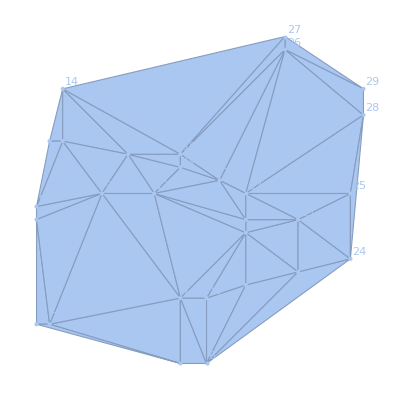

```mathematica
DelaunayMesh[pts,MeshCellLabel->{0->"Index"}]
```

Итоговый планарный граф выглядит таким образом:

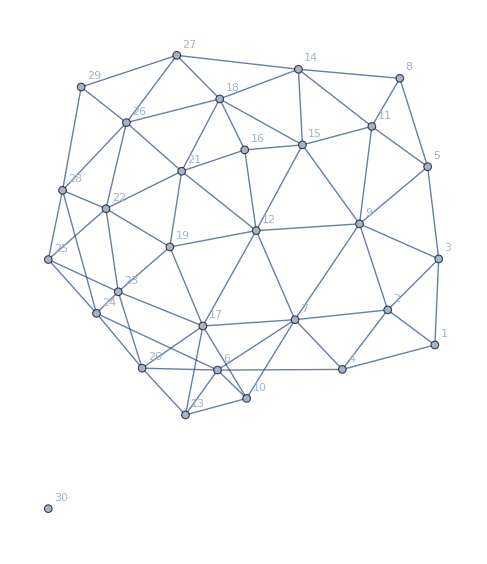

```mathematica
gr=planarGraph[pts]
```

```mathematica
PlanarGraphQ@gr
```

True

## Раскраска графа

```mathematica
(*Также есть глобальные переменные: x (список из цветов вершин графа,изначально состоящий из нулей) и listOfColors2 (это список списков всех "состояний" на протяжении работы алгоритма)*)

mat=AdjacencyMatrix[gr];
x=ConstantArray[0,Length@mat];
listOfColors2={};

colorChoose[k_, c_,matr_]:=
Module[{i=1,n=Length@matr,check=0},
While[i≤n,
If[matr⟦k,i⟧==1 && c==x⟦i⟧,
check=1];i++];
If[check≠0,False,True]]

graphColour[k_,matr_]:=
Module[{c=1,n=Length@matr},
While[c≤4,
If[colorChoose[k,c,matr],
x⟦k⟧=c;
If[x⟦n⟧==0,AppendTo[listOfColors2,x]];
If[(k+1)≤n,If[x⟦n⟧==0,
graphColour[k+1,matr]]]
];c++];x]
```

Следующий этап — раскраска полученного плоского графа. Для этого был реализован поиск с возвратом (или Backtracking), который, начиная с вершины k, проверяет соседние вершины на совпадение цветов с вершиной k, и если цвета совпадают, то проверяет возможность раскраски другим цветом; если же следующую вершину нельзя раскрасить ни в один цвет, алгоритм красит в другой цвет уже предыдущую и повторяет попытку. 

Вообще говоря, задача о раскраске графа является NP-полной: по сути, нужно выяснить, можно ли раскрасить данный граф m цветами (она не NP-полная для m=1 и m=2, однако в нашем случае m=4, так что данный факт очевиден). Это значит, что для данной задачи не существует идеального метода (алгоритма) решения, и, в частности, Backtraсking — не самый эффективный, но один из схожих с другими по эффективности способ раскраски. 

Данная функция имеет два аргумента: k (номер вершины, с которой начинается раскраска) и mat (матрица смежности планарного графа, сгенерированного ранее). На выходе — список “цветов”, т.е. чисел от 1 до 4...

```mathematica
graphColour[1,mat]
```

{4,2,3,3,1,4,1,2,4,3,3,2,1,4,1,3,4,2,1,3,4,3,2,1,4,1,3,2,4,4}

...или список, каждый элемент которого имеет вид {номер вершины -> цвет}:

```mathematica
rule=Rule@@@Transpose@{Range@Length@mat,Association[0->White,1->Red,2->Blue,3->Green,4->Yellow]/@graphColour[1,mat]}
```

{1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[0, 1, 0],4→RGBColor[0, 1, 0],5→RGBColor[1, 0, 0],6→RGBColor[1, 1, 0],7→RGBColor[1, 0, 0],8→RGBColor[0, 0, 1],9→RGBColor[1, 1, 0],10→RGBColor[0, 1, 0],11→RGBColor[0, 1, 0],12→RGBColor[0, 0, 1],13→RGBColor[1, 0, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 0, 0],16→RGBColor[0, 1, 0],17→RGBColor[1, 1, 0],18→RGBColor[0, 0, 1],19→RGBColor[1, 0, 0],20→RGBColor[0, 1, 0],21→RGBColor[1, 1, 0],22→RGBColor[0, 1, 0],23→RGBColor[0, 0, 1],24→RGBColor[1, 0, 0],25→RGBColor[1, 1, 0],26→RGBColor[1, 0, 0],27→RGBColor[0, 1, 0],28→RGBColor[0, 0, 1],29→RGBColor[1, 1, 0],30→RGBColor[1, 1, 0]}

Раскрашенный в процессе алгоритма граф выглядит так:

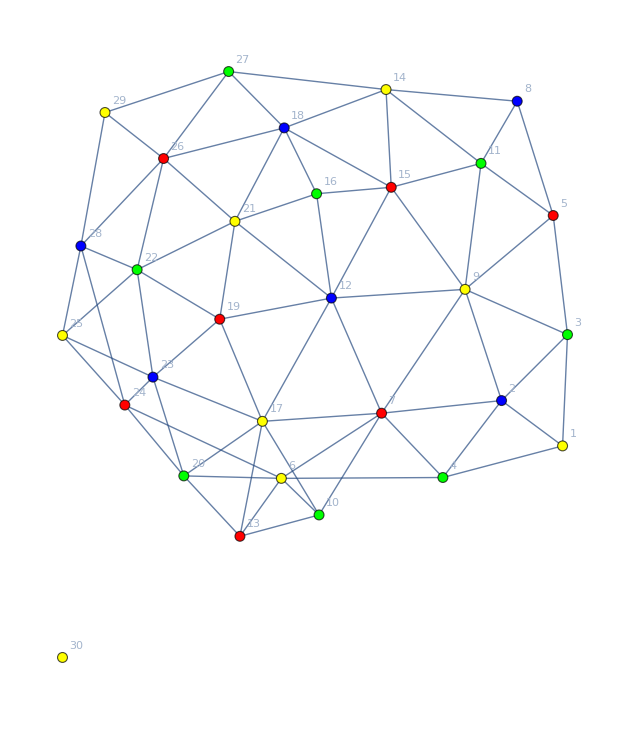

```mathematica
Graph[gr,VertexStyle->rule]
```

## Пошаговая визуализация раскраски графа

Здесь используем созданный прежде список списков, состоящий из всех “шагов” работы алгоритма раскраски.

```mathematica
AppendTo[listOfColors2,x];

Manipulate[Graph[gr,VertexStyle->Rule@@@Transpose@{Range@Length@listOfColors2,Association[0->White,1->Red,2->Blue,3->Green,4->Yellow]/@(listOfColors2⟦i⟧~Join~ConstantArray[0,Length@listOfColors2-Length@x])},ImageSize->Large],{i,1,Length@listOfColors2,1}]
```

## Раскраска графа, вершинами которого являются страны на карте

Переход от графов к картам. Здесь из базы Mathematica (если точнее, из CountryData) берётся какая-то часть карты мира — совокупность стран (и координаты центра каждой из них), и для этой совокупности строится соответствующий (очевидно, планарный) граф. 

Следующая функция принимает на вход список стран. По нему, зная — также благодаря базе данных Mathematica — координаты центра каждой страны (“CenterCoordinates”) и наличие границ между любыми двумя странами (“BorderingCountries”), функция строит граф, а затем раскрашивает его по написанному в одном из предыдущих пунктов алгоритму раскраски.
В итоге выводится, во-первых, список рёбер, который задаёт искомый граф, во-вторых, сам граф (опять же, соответствующий какой-то совокупности стран, в т.ч. целому континенту/континентам) с раскрашенными вершинами.

```mathematica
(*сюда скопирован код с изменёнными названиями алгоритма и глобальных переменных для корректной автоинициализации ячеек*)

xMap=ConstantArray[0,Length@Intersection[CountryData["Europe"],CountryData["UnitedNations"]]];
listOfColors3={};

colorChooseMap[k_, c_,matr_]:=
Module[{i=1,n=Length@matr,check=0},
While[i≤n,
If[matr⟦k,i⟧==1 && c==xMap⟦i⟧,
check=1];i++];
If[check≠0,False,True]]

graphColourMap[k_,matr_]:=
Module[{c=1,n=Length@matr},
While[c≤4,
If[colorChooseMap[k,c,matr],
xMap⟦k⟧=c;
If[xMap⟦n⟧==0,AppendTo[listOfColors3,xMap]];
If[(k+1)≤n,If[xMap⟦n⟧==0,
graphColourMap[k+1,matr]]]
];c++];
xMap]

graphColoring[countries_]:=Module[{orderCountries,rule,mapGraph={},graph,mat,colorsRuleMap,mapColors},orderCountries=SortBy[{#,Plus@@CountryData[#,"CenterCoordinates"]}&/@Intersection[CountryData[countries],CountryData["UnitedNations"]],Last];rule=Rule@@@Transpose@{Range@Length@orderCountries,orderCountries⟦All,1⟧};Table[If[IntersectingQ[CountryData[rule⟦i,2⟧,"BorderingCountries"],{rule⟦j,2⟧}] && i<j,AppendTo[mapGraph,i<->j]],{i,1,Length@rule},{j,1,Length@rule}];Print[mapGraph];mat=AdjacencyMatrix@Graph[Range@Length@orderCountries,mapGraph];graph=Graph[Range@Length@orderCountries,mapGraph,VertexLabels->"Name"];graphColourMap[1,mat];AppendTo[listOfColors3,graphColourMap[1,mat]];colorsRuleMap=Rule@@@Transpose@{Range@Length@mat,Association[0->White,1->Red,2->Blue,3->Green,4->Yellow]/@graphColourMap[1,mat]};mapColors=Rule@@@Transpose@{orderCountries⟦All,1⟧,colorsRuleMap⟦All,2⟧};Graph[graph,VertexStyle->colorsRuleMap,ImageSize->Large]];
```

{1<->2,2<->3,2<->6,3<->6,4<->9,6<->8,6<->10,6<->11,6<->12,6<->13,6<->17,10<->13,10<->16,10<->17,11<->12,11<->15,11<->17,11<->18,12<->14,12<->18,12<->20,13<->17,15<->18,16<->17,17<->18,17<->27,17<->28,17<->35,18<->20,18<->27,18<->29,18<->32,19<->20,19<->23,19<->24,19<->26,19<->29,20<->29,21<->22,21<->23,21<->25,22<->25,22<->30,23<->24,23<->26,24<->26,25<->26,25<->30,26<->29,26<->30,26<->33,27<->32,27<->35,29<->32,29<->33,29<->40,30<->33,32<->35,32<->40,33<->36,33<->40,34<->37,34<->43,35<->38,35<->39,35<->40,36<->40,37<->43,38<->39,38<->41,39<->40,39<->41,41<->42}

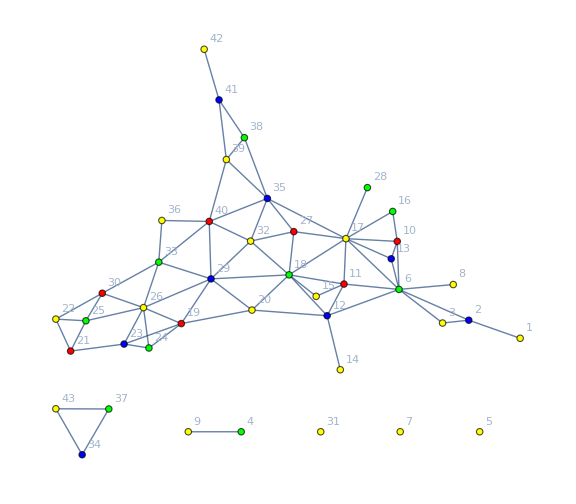

```mathematica
graphColoring["Europe"]
```

## Раскраска карт и пошаговая визуализация

Учитывая, что теперь имеется раскрашенный граф, соответствующий карте, то можно также раскрасить и данную карту.
Это действие осуществляет следующая функция, которая на вход также принимает совокупность стран, а выдаёт раскрашенную карту.

```mathematica
xMap=ConstantArray[0,Length@Intersection[CountryData["Europe"],CountryData["UnitedNations"]]];
listOfColors3={};

mapColoring[countries_]:=Module[{order,rule,mapGraph={},mat,colorsRule,mapColors},order=SortBy[{#,Plus@@CountryData[#,"CenterCoordinates"]}&/@Intersection[CountryData[countries],CountryData["UnitedNations"]],Last];rule=Rule@@@Transpose@{Range@Length@order,order⟦All,1⟧};Table[If[IntersectingQ[CountryData[rule⟦i,2⟧,"BorderingCountries"],{rule⟦j,2⟧}] && i<j,AppendTo[mapGraph,i<->j]],{i,1,Length@rule},{j,1,Length@rule}];mat=AdjacencyMatrix@Graph[Range@Length@order,mapGraph];graphColourMap[1,mat];AppendTo[listOfColors3,graphColourMap[1,mat]];colorsRule=Rule@@@Transpose@{Range@Length@order,Association[0->White,1->Red,2->Blue,3->Green,4->Yellow]/@graphColourMap[1,mat]};mapColors=Rule@@@Transpose@{order⟦All,1⟧,colorsRule⟦All,2⟧};GeoGraphics[{EdgeForm[Directive[Black,Thin]],{GeoStyling[#2],Tooltip[Polygon[#1],#1]}&@@@mapColors},ImageSize->Large]];
```

```mathematica
mapColoring["Europe"]
```

-Graphics-

Для визуализации раскраски карты так же, как и для графа, запоминались промежуточные значения цветов; бесцветные страны соответствуют цвету “прозрачный” (Transparent)

```mathematica
manipulateColoring[countries_]:=Module[{listOfColors,table,ord,tableOfColors},listOfColors=Prepend[listOfColors3,ConstantArray[0,Length@Intersection[CountryData[countries],CountryData["UnitedNations"]]]];table=Table[Association[0->Transparent,1->Red,2->Blue,3->Green,4->Yellow]/@listOfColors⟦i⟧,{i,1,Length@listOfColors}];ord=SortBy[{#,Plus@@CountryData[#,"CenterCoordinates"]}&/@Intersection[CountryData[countries],CountryData["UnitedNations"]],Last];tableOfColors=Table[Rule@@@Transpose@{ord⟦All,1⟧,table⟦i⟧},{i,1,Length@listOfColors}];Manipulate[GeoGraphics[{EdgeForm[Directive[Black,Thin]],{GeoStyling[#2],Tooltip[Polygon[#1],#1]}&@@@tableOfColors⟦i⟧},ImageSize->Large],{i,1,Length@listOfColors,1}]]
```

```mathematica
manipulateColoring["Europe"]
```